# WENO Smooth Indicators

## Notebook modified to implement a WENO limiter for CPR & DG methods

coded by Manuel Diaz, 2013.11.13
manuel.ade’at’gmail.com

```mathematica
Quit[]; (* Reset Mathematica Kernel *)
```

### Refs,

```mathematica
(* This Mathematica files is helpful to derive the coeficients to implement first and/or second order WENO based derivates following the ideas of the following references: *)
	(* 1. Shu; 'High order weighted essentially nonoscillatory schemes for convection dominated problems'. SIAM review 2009 *)
	(* 2. Also following ideas in the publication by RhysU@http://www.scribd.com/RhysU *)
```

```mathematica
(* INITIALIZE FUNCTIONS *)
	(* We need to build a list of uniform gridpoints with spacing Δx and fucntion values Subscript[f, i]. Use that list to build the j^th interpolating Polynomial for j ϵ {1,...,r} *)
```

### Building the Domain

Define Domain x ∈ [ a , b ],
We then divide it into ‘n’ small cells/elements

```mathematica
a= 0; b = 1; n = 10; nf = n+1; Δx = (b-a)/n;
```

```mathematica
Table [Subscript[x, i-1/2]=a+ i Δx,{i,0,n}]
```

{0,1/10,1/5,3/10,2/5,1/2,3/5,7/10,4/5,9/10,1}

Define Intervals I_j:

```mathematica
Table[Subscript[I, j]={Subscript[x, j-3/2],Subscript[x, j-1/2]},{j,1,n}]
```

{{0,1/10},{1/10,1/5},{1/5,3/10},{3/10,2/5},{2/5,1/2},{1/2,3/5},{3/5,7/10},{7/10,4/5},{4/5,9/10},{9/10,1}}

Define element sizes h_j:

```mathematica
Table[Subscript[h, j]=(Subscript[x, j-1/2]-Subscript[x, j-3/2]),{j,1,n}]
```

{1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10,1/10}

Define element centers x_j :

```mathematica
Table[Subscript[x, j]=(Subscript[x, j-3/2]+Subscript[x, j-1/2])/2,{j,1,n}]
```

{1/20,3/20,1/4,7/20,9/20,11/20,13/20,3/4,17/20,19/20}

Standar Element Definition I_ξ:

```mathematica
Subscript[I, ξ] = ({{-1, 1}})
```

{{-1,1}}

Therefore the Jacobian metric between this two elements is given by,

```mathematica
J = Subscript[h, j]/2;
```

Now, let us define solution points, ξ_k, inside the standar element:
Lets define a polynomial of degree K=3 on either Legendre / Lobatto points,

```mathematica
K=3;
```

#### Build Gauss Lobatto Points

Generating up to 4th degree Legendre Polynomials.

```mathematica
legendreP = Table[LegendreP[i,x],{i,0,5}];
```

```mathematica
Table[Subscript[p, i]= legendreP[[i+1]],{i,0,5}];
{Subscript[p, 0],Subscript[p, 1],Subscript[p, 2],Subscript[p, 3],Subscript[p, 4],Subscript[p, 5]}
```

{1,x,1/2 (-1+3 x^2),1/2 (-3 x+5 x^3),1/8 (3-30 x^2+35 x^4),1/8 (15 x-70 x^3+63 x^5)}

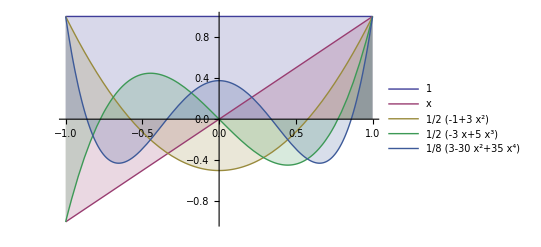

```mathematica
Plot[Evaluate[Most[legendreP]],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

Legendre Roots

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[p, 4]==0,x][[All,2]],Greater]
```

{-√(1/35 (15+2 √30)),-√(1/35 (15-2 √30)),√(1/35 (15-2 √30)),√(1/35 (15+2 √30))}

#### Legendre-Gauss-Lobatto (LGL) Polynomials

```mathematica
lobatto = Table[Subscript[p, k]-Subscript[p, k-2],{k,2,5}] //Simplify;
```

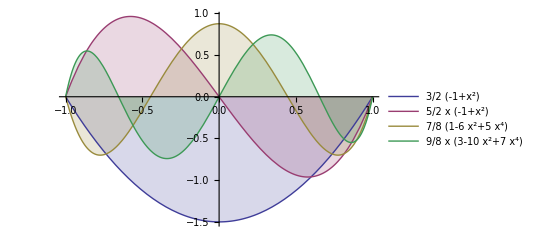

```mathematica
Plot[Evaluate[lobatto],{x,-1,1},Filling->Axis,PlotLegends->"Expressions"]
```

```mathematica
Table[Subscript[Lo, i]= lobatto[[i]],{i,1,4}]//TableForm
```

3/2 (-1+x^2)
5/2 x (-1+x^2)
7/8 (1-6 x^2+5 x^4)
9/8 x (3-10 x^2+7 x^4)

Lobatto Roots

```mathematica
abscissas = -Sort[List @@ Roots[Subscript[Lo, 3]==0,x][[All,2]],Greater]
```

{-1,-1/(√5),1/(√5),1}

I, personally, prefer to call the abscissas ‘standard solution points’ or simply ‘solution points’. I will also  referer to all the points inside the domain as my ‘global nodes coordinates’.

```mathematica
{Subscript[ξ, 1],Subscript[ξ, 2],Subscript[ξ, 3],Subscript[ξ, 4]}=abscissas; (* also the local coordinates inside Subscript[I, j] *)
```

Define Subpolynomial Domains over our original Domain. We  define the following mapping for x and ξ (solution points here) :

```mathematica
Subscript[x, 𝒟]=Table[Subscript[x, j]+ J ×abscissas,{j,1,n}];
Subscript[x, 𝒟]//TableForm//N
```

0. | 0.0276393 | 0.0723607 | 0.1
0.1 | 0.127639 | 0.172361 | 0.2
0.2 | 0.227639 | 0.272361 | 0.3
0.3 | 0.327639 | 0.372361 | 0.4
0.4 | 0.427639 | 0.472361 | 0.5
0.5 | 0.527639 | 0.572361 | 0.6
0.6 | 0.627639 | 0.672361 | 0.7
0.7 | 0.727639 | 0.772361 | 0.8
0.8 | 0.827639 | 0.872361 | 0.9
0.9 | 0.927639 | 0.972361 | 1.

Define ' u_(j,k)’ values for every node in our domain.
I will assume an IC as: u(x) = 0.5 +sin(2πx), therefore

```mathematica
Table[Subscript[x, j,k]= Subscript[x, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

```mathematica
(*Subscript[u, 𝒟]=0.5(2+Sin[2 π Subscript[x, 𝒟]]);*)
riemann[x_]:= Piecewise[{{2,x<=0.45},{1,x>0.45}}];
Subscript[u, 𝒟] = Table[riemann[Subscript[x, j,k]],{j,1,10},{k,1,4}];
Subscript[u, 𝒟]//TableForm
```

2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 2 | 2
2 | 2 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1
1 | 1 | 1 | 1

Load u_0 into our domain

```mathematica
Table[Subscript[u, j,k]= Subscript[u, 𝒟][[j,k]],{j,1,n},{k,1,4}];
```

take for example j=4 and k=1, we should get

```mathematica
Subscript[u, 4,1]
```

2

#### Continuous Case

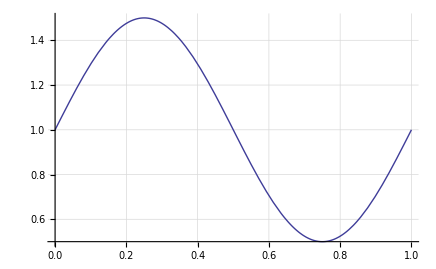

```mathematica
u[x_,t_]:= 0.5(2+Sin[2π x]);
sin =Plot[u[x,t],{x,0,1},PlotRange->Full,GridLines->Automatic]
```

#### Discontinuous Case

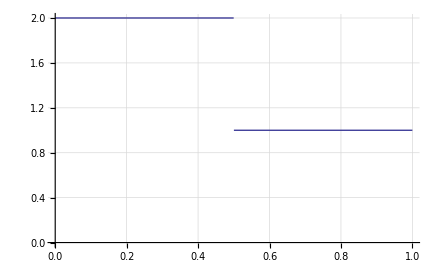

```mathematica
u[x_,t_]:= Piecewise[{{2,x<0.5},{1,x>=0.5}}]
Plot[u[x,t],{x,0,1},PlotRange->{0,2},GridLines->Automatic]
```

Assume t = 0. Evaluate u[x, t] at discrete value points,

### Build Lagrange Polynomials u_j(x) for every cell in the Domain

#### Polynomail Stencils

```mathematica
LagrangeStencil[j_]:= Table[{Subscript[x, j,k],Subscript[u, j,k]},{k,1,4}]
```

```mathematica
LagrangePolynomial[j_] := InterpolatingPolynomial[LagrangeStencil[j],x]
```

#### Testing Stencils

```mathematica
LagrangeStencil[1]//N
```

{{0.,2.},{0.0276393,2.},{0.0723607,2.},{0.1,2.}}

```mathematica
LagrangePolynomial[1]//Expand
```

2

### Smooth Indicators

Here we use the classical expresion proposed in ref [2]:

β_j=∑_(l=1)^k ∫_(x_(i-1/2))^(x_(i+1/2)) (Δx^(2l-1)((∂^l p_j[x])/(∂x^l)))^2 ⅆx ,         where k is the polynomial degree.

```mathematica
StencilSmoothness[j_,K_]:=Together[Expand[Sum[Δx^(2d-1)Integrate[D[LagrangePolynomial[j],{x,d}]^2,{x,Subscript[x, j,1],Subscript[x, j,1+K]}],{d,K}]]]
```

```mathematica
(* Check Smoothness indicartors against the result Matlab Implementation *)
```

```mathematica
Subscript[β, 1]=StencilSmoothness[1,K];
Subscript[β, 2]=StencilSmoothness[2,K];
Subscript[β, 3]=StencilSmoothness[3,K];
Subscript[β, 1]//N
Subscript[β, 2]//N
Subscript[β, 3]//N
```

0.

0.

0.

### Numerical Test

for this cases we know the gamma and epsilon values to be,

```mathematica
{Subscript[γ, 1],Subscript[γ, 2],Subscript[γ, 3]} = {0.000001,0.999998,0.000001}; ϵ = 10^-6;
```

Evaluating every point/cell in the domain,

```mathematica
j=5;
LagrangeStencil[5]//N
```

{{0.4,2.},{0.427639,2.},{0.472361,1.},{0.5,1.}}

```mathematica
{Subscript[β, 1],Subscript[β, 2],Subscript[β, 3]}={
StencilSmoothness[j-1,K],
StencilSmoothness[j,K],
StencilSmoothness[j+1,K]
}//N
ω= Table[Subscript[γ, j]/(ϵ+Subscript[β, j])^2,{j,1,3}];ω//N
w = Table[ω[[j]]/Total[ω],{j,3}]
```

{0.,1492.58,0.}

{1.×10^6,4.48875×10^-7,1.×10^6}

{0.5,2.24438×10^-13,0.5}

Observer the behavior of the WENO smooth indicators in continuous and discontinuous data!